```mathematica
ClearAll["Global`*"]
```

```mathematica
(*solve with mathematica*)
```

```mathematica
(*u[x]_here = u_2[x]_notes*)
```

```mathematica
(*F_here =  F_{22}_notes*)
```

```mathematica
F[x_]:=1 + u'[x]
```

```mathematica
(*EE[x]_here  = E_22_notes*)
```

```mathematica
EE[x_]:=1/2(F[x]^2-1)
```

```mathematica
(*S[x]_here = S_{22}_notes*)
```

```mathematica
S[x_]:=(K+μ)EE[x]
```

```mathematica
(*P[x]_here  = P_{22}_notes*)
```

```mathematica
P[x_]:=F[x]S[x]
```

```mathematica
P[x]
```

1/2 (K+μ) (1+u'[x]) (-1+(1+u'[x])^2)

```mathematica
(*
The condition P[L]==0 has multiple solutions-> we pick the solution u'[L]==0
*)
```

```mathematica
L=1;
K=1.25;
μ=1;
ρy[x_]:=1;
g=5/100;
```

```mathematica
sol=NDSolve[{P'[x]+ρy[x]g==0,u[0]==0,u'[L]==0},u,{x,0,L}][[1]]
```

{u→InterpolatingFunction[…]}

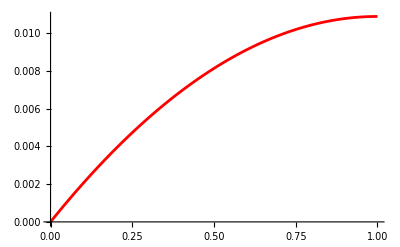

```mathematica
plotmathematica=Plot[u[x]/.sol,{x,0,L},PlotStyle->Red]
```

```mathematica
(*import the solution with python*)
```

```mathematica
tab=Import["/Users/michelecastellana/Documents/finite_elements/elasticity/rod/steady_state/solution/u.csv"]
tab=Drop[tab,{1}]
```

```mathematica
tab=Table[{tab[[i,4]],tab[[i,1]]},{i,1,Length[tab]}]
```

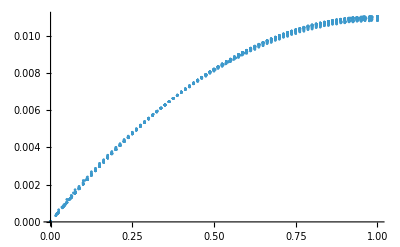

```mathematica
ListPlot[tab]
```

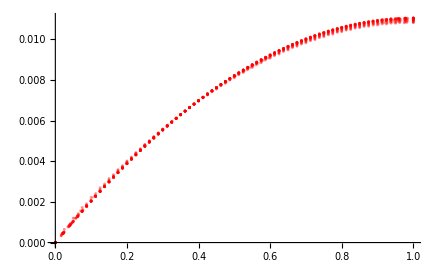

```mathematica
plotpython=ListPlot[tab,PlotStyle->{Red, Opacity->0.25}]
```

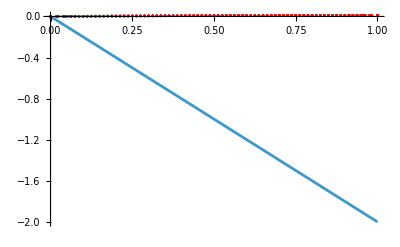

```mathematica
Show[plotmathematica,plotpython]
```